# Rescaled f(R)Canonical Scalar Field Inflation In The Presence Of A Chern-Simons Term.

## Chaotic Inflation With A Power-Law Chern-Simons Scalar Coupling Function.

## 1.Designation Of Scalar Functions, Equations Of Motion, Slow-Roll/Observed Indices.

We start by designating the scalar functions of the model. For simplicity, the Chern-Simons scalar coupling function obtains a power-law form along with the scalar potential. Compatibility is achieved for a quadratic potential but we shall keep it arbitrary for the time being so as to study the dependence of the observed indices, and especially the scalar spectral index ns on such exponent. The equations of motion are extracted by assuming the slow-roll condition is valid. Slow-roll indices along with observed indices are taken from arXiv:0412126.

Every parameter that ends with 1 is an auxiliary free parameter that needs to be designated later. With v and V the Chern-Simons coupling and the scalar potential are denoted while H is Hubble’s parameter and H2 the squared Hubble. Each parameter ending with dot implies time derivative for simplicity and Qt is an auxiliary function that depends on both the scalar field and the polarization of gravitational waves. Finally, indices ε1 through ε3 are the slow-roll indices of the model and ns, nt, r indicate the observed indices.

```mathematica
v[φ_]:=Λ1 (κ φ)^p
vdot[φ_]:=D[v[φ],φ]φdot[φ]
V[φ_]:=V1(κ φ)^n
H2[φ_]:=κ^2 V[φ]/(3α)
H[φ_]:=Sqrt[H2[φ]]
φdot[φ_]:=(-D[V[φ],φ])/(3H[φ])
Hdot[φ_]:=-κ^2/(2α)φdot[φ]^2
Qt[λ_,φ_]:=α/κ^2+2λ vdot[φ]H[φ]
ε1[φ_]:=(-Hdot[φ])/H2[φ]
ε2[φ_]:=ε1[φ]-α D[V[φ],{φ,2}]/(κ^2 V[φ])
ε6[φ_]:=(D[Qt[1,φ],φ]φdot[φ])/(2H[φ]Qt[1,φ])+(D[Qt[-1,φ],φ]φdot[φ])/(2H[φ]Qt[-1,φ])
ns[φ_]:=1-2(2ε1[φ]+ε2[φ])
nt[φ_]:=-2(ε1[φ]+ε6[φ])
r[φ_]:=8Abs[ε1[φ]](α/Abs[κ^2 Qt[1,φ]]+α/Abs[κ^2 Qt[-1,φ]])
```

## 2. Extracting The Values Of The Scalar Field.

To study the inflationary era, one needs to insert as an input the value of the scalar field during the first horizon crossing to the observed indices. Such a value can be extracted by firstly finding the final value during the ending stage of the inflationary era by imposing that ε1 becomes of order O(1). Afterwards, by using the e-folding number N=∫ Hdt, the initial value can be extracted as a function of N and φf.

I use variable U to denote solutions hereafter while L is a random variable such that the initial value of the scalar field can be extracted.

```mathematica
U1=Solve[ε1[φ]==1,φ];
φf=φ/.U1[[2]]/.C[1]->0;
L1=Integrate[H[φ]/φdot[φ],φ]/.φ->φl;
L2=Integrate[H[φ]/φdot[φ],φ]/.φ->φk;
U2=Solve[N0==L1-L2,φk];
φi=φk/.U2[[2]]/.{C[1]->0,φl->φf};
```

## 3. Designation Of Free Parameters And Validity Of Approximations.

### 3.1. Derivation Of Observed Indices.

By assigning numerical values to the free parameters of the model, the initial value of the scalar field during the first horizon crossing is extracted. Subsequently, one can use such value as an input on the observed indices and derive results. Here, a blue shifted tensor spectral index (nt>0) can be achieved under the slow-roll assumption due to the presence of the Chern-Simons term in the initial gravitational action.

```mathematica
κ=1/Mp;Mp=1; Λ1=1;V1=Mp^4;N0=60.;n=2;p=2;α=0.001;
φi/Mp//N
φf/Mp//N
ns[φ]/.φ->φi//N
nt[φ]/.φ->φi//N
r[φ]/.φ->φi//N
φf-φi//N
D[V[φ],φ]/V[φ]/.φ->φi//N
-D[V[φ],{φ,2}]/V[φ]/.φ->φi//N
```

0.491935

0.0447214

0.966942

0.016529

0.000204905

-0.447214

4.06558

-8.26446

### 3.2. Observed Indices

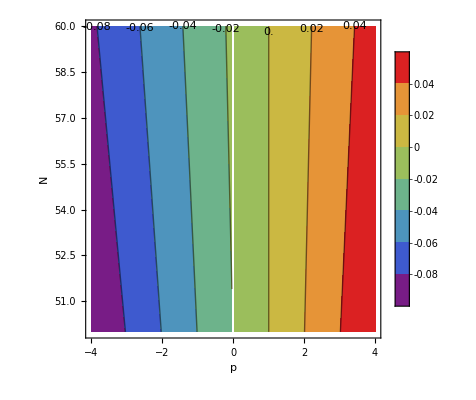

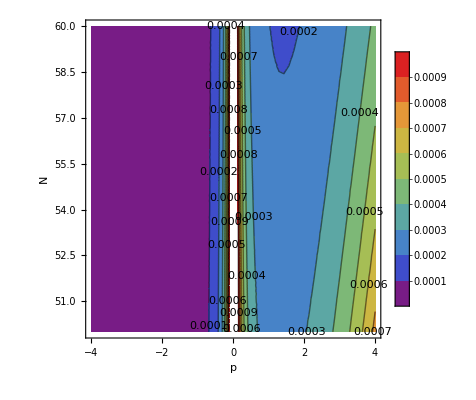

```mathematica
Clear[p];Clear[N0];
ContourPlot[Evaluate[nt[φ]/.φ->φi],{p,-4,4},{N0,50.,60.},PlotLegends->True,FrameLabel->{"p","N"},ColorFunction->{"Rainbow"},ContourLabels->True]
ContourPlot[Evaluate[r[φ]/.φ->φi],{p,-4,4},{N0,50.,60.},PlotLegends->True,FrameLabel->{"p","N"},ColorFunction->{"Rainbow"},ContourLabels->True]
```

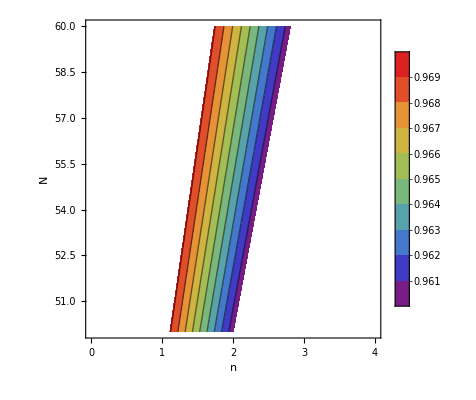

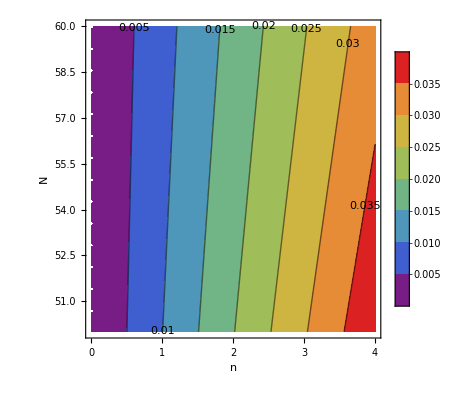

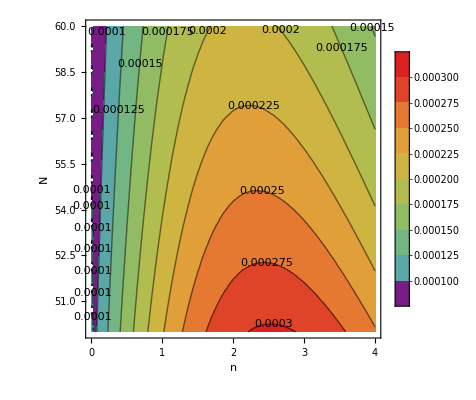

```mathematica
α=0.0014;p=2;
Clear[n,N0]
ContourPlot[Evaluate[ns[φ]/.φ->φi],{n,0,4},{N0,50.,60.},PlotLegends->True,FrameLabel->{"n","N"},PlotRange->{0.9646-0.0042,0.9649+0.0042},ColorFunction->{"Rainbow"}]
ContourPlot[Evaluate[nt[φ]/.φ->φi],{n,0,4},{N0,50.,60.},PlotLegends->True,FrameLabel->{"n","N"},ColorFunction->{"Rainbow"},ContourLabels->True]
ContourPlot[Evaluate[r[φ]/.φ->φi],{n,0,4},{N0,50.,60.},PlotLegends->True,FrameLabel->{"n","N"},ColorFunction->{"Rainbow"},ContourLabels->True]
N0=60;Clear[α];
ContourPlot[Evaluate[ns[φ]/.φ->φi],{n,0,4},{α,0.0001,0.1},PlotLegends->True,FrameLabel->{"n","α"},PlotRange->{0.9646-0.0042,0.9649+0.0042}];
ContourPlot[Evaluate[nt[φ]/.φ->φi],{n,0,4},{α,0.0001,0.1},PlotLegends->True,FrameLabel->{"n","α"},PlotRange->{0,0.064}];
ContourPlot[Evaluate[r[φ]/.φ->φi],{n,0,4},{α,0.0001,0.1},PlotLegends->True,FrameLabel->{"n","α"}];
n=2;Clear[N0];
ContourPlot[Evaluate[ns[φ]/.φ->φi],{α,0.0001,0.1},{N0,50.,60.},PlotLegends->True,FrameLabel->{"n","N"},PlotRange->{0.9646-0.0042,0.9649+0.0042}];
ContourPlot[Evaluate[nt[φ]/.φ->φi],{α,0.0001,0.1},{N0,50.,60.},PlotLegends->True,FrameLabel->{"n","N"}];
ContourPlot[Evaluate[r[φ]/.φ->φi],{α,0.0001,0.1},{N0,50.,60.},PlotLegends->True,FrameLabel->{"n","N"}];
```

### 3.2. Swampland Criteria.

Before proceeding, always remember that the Swampland criteria are not affected by the Chern-Simons terms since it affects only tensor perturbations. It does not influence even the evolution of the inflaton with respect to time! So the criteria for a canonical scalar potential are universal with respect to the e-folding number N and the amplitude V1 of the potential. Hence, if the criteria are not in agreement with the scalar spectral index, there is nothing we can do however if they are not in agreement with the tensor-to-scalar ratio and the tensor spectral index, one can manipulate the Chern-Simons term to obtain a viable description. Since in most cases the scalar spectral index seems to not be in agreement with the third Swampland criterion, it would be worth examining how one can affect scalar perturbations, and the easiest ways possible would be to either introduce a non-minimal coupling between the scalar field and the Ricci scalar (it should not be irrational as the Chern-Simons coupling is already a coupling between curvature and the scalar field) or introduce something new in the kinetic term, for instance add a higher order kinetic term, make the theory k-essence, add an exotic term such as Dirac-Born-Infeld and so on. It would just be more perplexed, and the theory at hand is already “too much” since it has an f(R) term which just produces this α prefactor. in the early universe via Taylor. The non-minimal coupling should perhaps be considered in a future work.

  
The first criterion is satisfied either for a small α and arbitrary exponent of the scalar potential, or arbitrary prefactor α but small exponent (roughly speaking below 1/10)

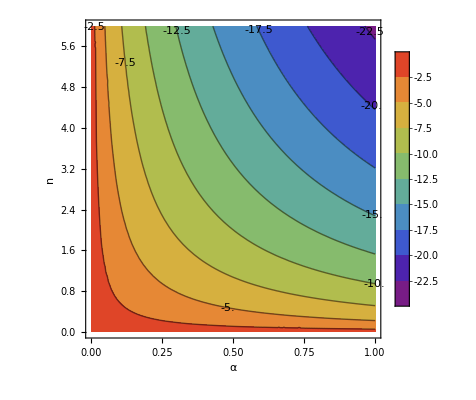

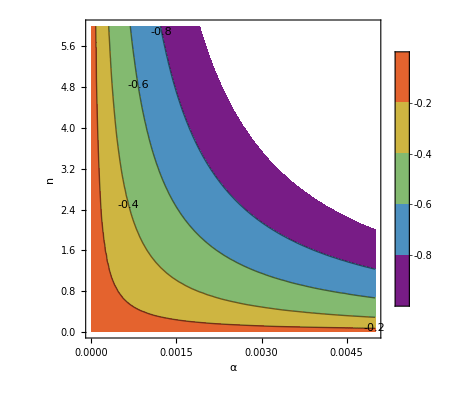

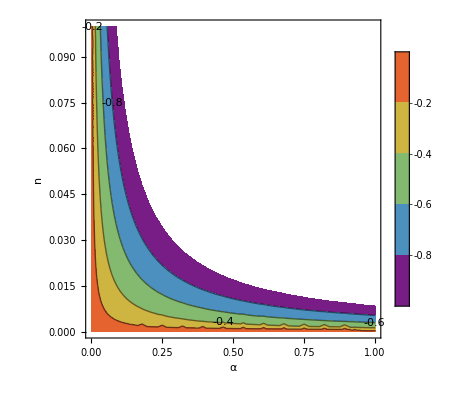

```mathematica
N0=60;  Clear[α,φ1,V1,Λ1,n,κ,p]
 κ=1;
Δφ=φf-φi;
ContourPlot[Δφ,{α,0,1},{n,0,6},FrameLabel->{"α","n"},ContourLabels->All,PlotLegends->Automatic,ColorFunction->"Rainbow"]
ContourPlot[Δφ,{α,0,0.005},{n,0,6},FrameLabel->{"α","n"},ContourLabels->All,PlotLegends->Automatic,ColorFunction->"Rainbow",PlotRange->{-1,1}]
ContourPlot[Δφ,{α,0,1},{n,0,0.1},FrameLabel->{"α","n"},ContourLabels->All,PlotLegends->Automatic,ColorFunction->"Rainbow",PlotRange->{-1,1}]
```

Now the second criterion can be valid for a wide variety so it does not pose a problem. It needs no consideration.

4.06558

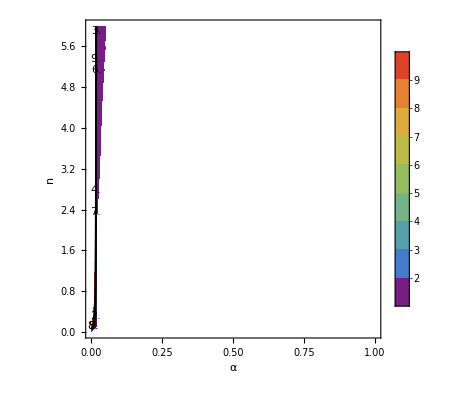

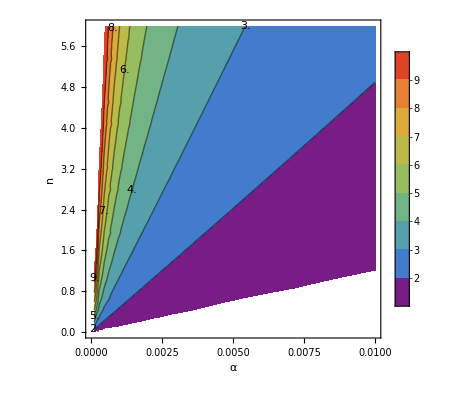

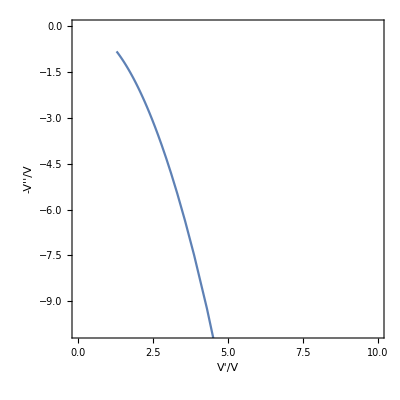

```mathematica
V'[φi]/V[φi]/.{n->2,α->0.001} 
ContourPlot[V'[φi]/V[φi],{α,0,1},{n,0,6},FrameLabel->{"α","n"},ContourLabels->All,PlotLegends->Automatic,ColorFunction->"Rainbow",PlotRange->{1,10}]
ContourPlot[V'[φi]/V[φi],{α,0.0001,0.01},{n,0,6},FrameLabel->{"α","n"},ContourLabels->All,PlotLegends->Automatic,ColorFunction->"Rainbow",PlotRange->{1,10}]
n=2;
ParametricPlot[{Evaluate[D[V[φ],φ]/V[φ]/.φ->φi],Evaluate[-D[V[φ],{φ,2}]/V[φ]/.φ->φi]},{α,0.0001,0.01},Frame->True,FrameLabel->{"V'/V","-V''/V"},PlotRange->{{0,10},{-10,0}}]
Clear[n];
```

Finally, the third criterion can be satisfied for quite small values of α but the exponent must be lesser than unity. This is quite interesting and keep in mind that is independent of the Chern-Simons scalar coupling functions since now such parameter participates in the EoMs or the first slow-roll index. This statement is essentially at variance with the viability of the scalar spectral index thus they cannot be satisfied simultaneously.

-8.26446

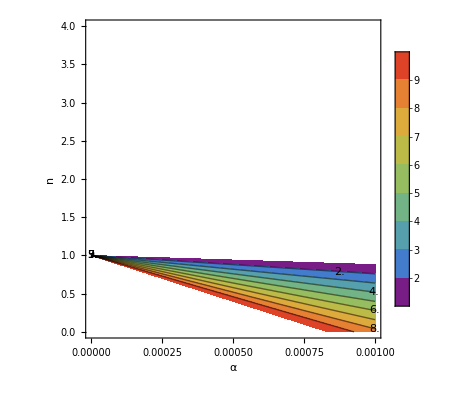

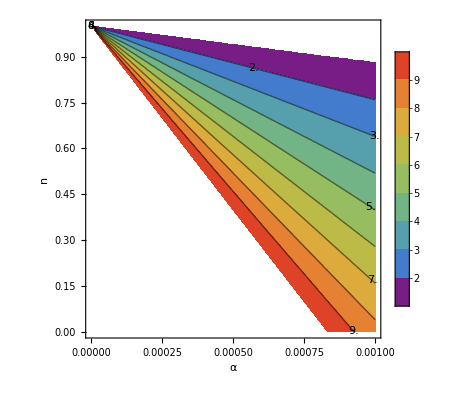

```mathematica
-V''[φi]/V[φi]/.{n->2,α->0.001}//N
ContourPlot[-V''[φi]/V[φi],{α,0,0.001},{n,0,4},FrameLabel->{"α","n"},ContourLabels->All,PlotLegends->Automatic,ColorFunction->"Rainbow",PlotRange->{1,10}]
ContourPlot[-V''[φi]/V[φi],{α,0,0.001},{n,0,1},FrameLabel->{"α","n"},ContourLabels->All,PlotLegends->Automatic,ColorFunction->"Rainbow",PlotRange->{1,10}]
```

### 3.3. Ascertaining The Validity Of The Approximations.

The numerical values of the slow-roll indices during the first horizon crossing according to Planck 2018 data must be of order O(10^-3) and lesser. Such results are indicative of the validity of the slow-roll approximations. Slow-roll index ε6 is excluded in this case.

```mathematica
κ=1/Mp;Mp=1; Λ1=1.;V1=Mp^4;N0=60.;n=2.;p=2.;α=0.001;
ε1[φ]/.φ->φi//N
ε2[φ]/.φ->φi//N
ε6[φ]/.φ->φi//N
```

0.00826446

1.79207×10^-18

-0.016529

Such result is also expected to apply on the self check on the equations of motion.

```mathematica
Hdot[φ]/.φ->φi//N
H2[φ]/.φ->φi//N
φdot[φ]^2/2/.φ->φi//N
V[φ]/.φ->φi//N
D[φdot[φ],φ]φdot[φ]/.φ->φi//N
H[φ]φdot[φ]/.φ->φi//N
```

-0.666667

80.6667

0.000666667

0.242

-5.06745×10^-19

-0.327957